# Nirmatrelvir experiments

Drug concentration in the stomach: sigma
Drug concentration at the epithelial lung cells: Ni

The dynamic is described by the following ODEs:

```mathematica
DSolve[{sigma'[t]==-alpha*sigma[t],Ni'[t]==alpha*sigma[t]-beta*Ni[t]},{sigma,Ni},t]
```

{{Ni→Function[{t},ⅇ^(-beta t) C[1]-(alpha ⅇ^(-alpha t-beta t) (-ⅇ^(alpha t)+ⅇ^(beta t)) C[2])/(alpha-beta)],sigma→Function[{t},ⅇ^(-alpha t) C[2]]}}

## Ritonavir-boosted nirmatrelvir:

Data points are from https://www.medrxiv.org/content/10.1101/2022.02.08.22270649v1.full.pdf

```mathematica
dataRN ={{0.5,700},{1.5,1800},{2,2000},{2.5,2300},{4,2800},{6,2100},{8,1800},{12,700},{24,200},{48,8}};
```

We need to fit to minutes, not hours:

```mathematica
dataRN = Map[{#[[1]]*60, #[[2]]}&, dataRN];
```

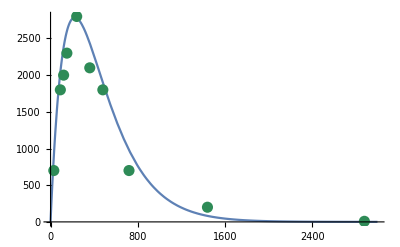

```mathematica
alpha = 0.005;
beta = 0.004;
c1 = 0;
c2=6800;
Show[Plot[c1*Exp[-beta*t]-(alpha*c2*(-Exp[-beta*t]+Exp[-alpha*t]))/(alpha-beta),{t,0,3000},PlotRange->All],ListPlot[dataRN,PlotStyle->Directive[ColorData["Legacy","SeaGreen"],PointSize[0.02]]]]
```

## Nirmatrelvir only, no ritonavir

Data points are from https://www.medrxiv.org/content/10.1101/2022.02.08.22270649v1.full.pdf

```mathematica
dataN=Map[{#[[1]]*60, #[[2]]}&,{{1,700},{2,600},{2.5,500},{4,230},{6,200},{8,100},{11,70},{48,13}}];
```

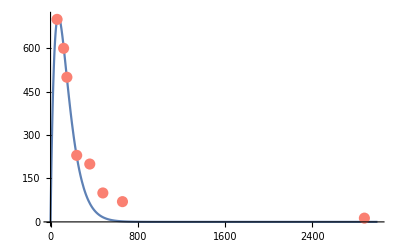

```mathematica
alpha = 0.015;
beta = 0.013;
c1 = 0;
c2=1800;
Show[Plot[c1*Exp[-beta*t]-(alpha*c2*(-Exp[-beta*t]+Exp[-alpha*t]))/(alpha-beta),{t,0,3000},PlotRange->All],ListPlot[dataN,PlotStyle->Directive[ColorData["Legacy","Salmon"],PointSize[0.02]]]]
```